```mathematica
Labelify[list_]:=Map[SymbolToLabel[#]&,list]
```

```mathematica
Table[
{ShowGraph[allGraphs5,k],Labelify[FlatGenerators[allGraphs5[k,"colofour"]]]}->
TableForm[
Table[
{ShowGraph[allGraphs5,child[[1]]],Labelify[FlatGenerators[allGraphs5[child[[1]],"colofour"]]],ShowGraph[allGraphs5,child[[2]]],Labelify[FlatGenerators[allGraphs5[child[[2]],"colofour"]]]}
,{child,allGraphs5[k,"children"]}]
],{k,Take[Select[Keys[allGraphs5],MaximalPlanarQ[allGraphs5[#,"graph"]]&],5]}]
```

{{-Graphics-29523,{1♁2♁3♁45}}→-Graphics-29524 | 1♁2♁3♁4♁5 | -Graphics-29525 | 1♁2♁3♁45,{-Graphics-29525,{1♁2♁3♁45}}→{},{-Graphics-29527,{1♁2♁35♁4}}→{},{-Graphics-29521,{1♁2♁35♁4}}→-Graphics-29524 | 1♁2♁3♁4♁5 | -Graphics-29527 | 1♁2♁35♁4,{-Graphics-29533,{1♁2♁34♁5}}→{}}

```mathematica
max6=Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&&MaximalPlanarQ[allGraphs6[#,"graph"]]&];
```

```mathematica
max6bis=Map[First,Tally[max6,IsomorphicGraphQ[allGraphs6[#1,"graph"],allGraphs6[#2,"graph"]]&]]
```

{7174416,7112974}

```mathematica
TableForm[
Table[
Framed[
Labeled[
TableForm[
Table[
{
With[{a=First[Select[allGraphs6[child[[2]],"vertexsets"],Length[#]==2&]]},
UndirectedEdge[a[[1]],a[[2]]]
],
ShowGraph[allGraphs6,child[[1]]],
Labelify[FlatGenerators[allGraphs6[child[[1]],"colofour"]]],
ShowGraph[allGraphs6,child[[2]]],
Labelify[FlatGenerators[allGraphs6[child[[2]],"colofour"]]]
}
,{child,allGraphs6[k,"children"]}]
],
Row[{ShowGraph[allGraphs6,k],Labelify[FlatGenerators[allGraphs6[k,"colofour"]]]}],Top
]
],{k,max6bis}]
]
```

3<->6 | -Graphics-7174443 | 1♁2♁3♁4♁56
1♁2♁3♁45♁6 | -Graphics-7174471 | 1♁2♁36♁45
4<->5 | -Graphics-7174425 | 1♁2♁3♁4♁56
1♁2♁36♁4♁5 | -Graphics-7174435 | 1♁2♁36♁45
5<->6 | -Graphics-7174417 | 1♁2♁36♁45 | -Graphics-7174454 | 1♁2♁3♁4♁56-Graphics-7174416{1♁2♁36♁45,1♁2♁3♁4♁56}
1<->6 | -Graphics-7172023 | 1♁25♁34♁6 | -Graphics-7231072 | 16♁25♁34
2<->5 | -Graphics-7115161 | 16♁2♁34♁5 | -Graphics-7117348 | 16♁25♁34
3<->4 | -Graphics-7113217 | 16♁25♁3♁4 | -Graphics-7113460 | 16♁25♁34-Graphics-7112974{16♁25♁34}

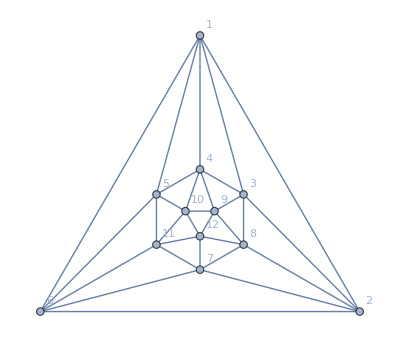

```mathematica
pl1=Graph[plantri[[1]],VertexLabels->"Name", GraphLayout->"TutteEmbedding"]
```

```mathematica
ffpl1=FindFullFormula[pl1];
```

```mathematica
pl1gen=Select[ffpl1,StringCount[SymbolName[#],"x"]==3&]
```

{v19bx25cx37ax468,v19bx24cx357x68a,v18ax29bx357x46c,v18bx259x37ax46c,v18bx24cx36ax579,v18ax24bx36cx579,v17ax29bx35cx468,v17ax259x36cx48b,v179x25cx36ax48b,v179x24bx35cx68a}

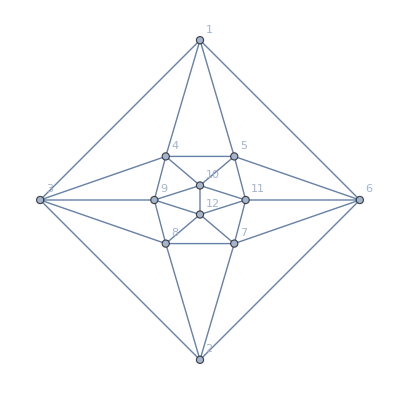

```mathematica
pl2=EdgeDelete[pl1,1<->2]
```

```mathematica
ChromaticPolynomial[pl1,7]
```

76848240

```mathematica
Table[ChromaticPolynomial[pl1,k]/k!,{k,4,12}]
```

{10,670,5573,45743/3,245669/12,198595/12,655057/72,9277343/2520,23348933/20160}

```mathematica
ffpl2=FindFullFormula[pl2];
```

```mathematica
pl2gen=Select[ffpl2,StringCount[SymbolName[#],"x"]==3&]
```

{v19bx25cx37ax468,v19bx24cx357x68a,v18ax29bx357x46c,v18bx259x37ax46c,v18bx24cx36ax579,v18ax24bx36cx579,v17ax29bx35cx468,v17ax259x36cx48b,v179x25cx36ax48b,v179x24bx35cx68a,v129bx37ax468x5c,v129bx37ax46cx58,v12cx36ax48bx579,v12ax36cx48bx579,v129bx357x4cx68a,v129bx35cx47x68a,v129bx357x46cx8a,v129bx35cx468x7a}

```mathematica
Tally[Map[StringCount[SymbolName[#],"x"]&,ffpl1]]//Sort
```

{{3,10},{4,660},{5,4908},{6,10008},{7,7900},{8,2800},{9,470},{10,36},{11,1}}

```mathematica
Tally[Map[StringCount[SymbolName[#],"x"]&,ffpl3]]//Sort
```

{{3,8},{4,299},{5,1448},{6,2074},{7,1145},{8,273},{9,28},{10,1}}

```mathematica
Tally[Map[StringCount[SymbolName[#],"x"]&,ffpl2]]//Sort
```

{{3,18},{4,959},{5,6356},{6,12082},{7,9045},{8,3073},{9,498},{10,37},{11,1}}

```mathematica
(Most[Tally[Map[StringCount[SymbolName[#],"x"]&,ffpl1]]//Sort])+(Tally[Map[StringCount[SymbolName[#],"x"]&,ffpl3]]//Sort)
```

{{6,18},{8,959},{10,6356},{12,12082},{14,9045},{16,3073},{18,498},{20,37}}

```mathematica
EdgeList[pl1]//Sort
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->3,2<->6,2<->7,2<->8,3<->4,3<->8,3<->9,4<->5,4<->9,4<->10,5<->6,5<->10,5<->11,6<->7,6<->11,7<->8,7<->11,7<->12,8<->9,8<->12,9<->10,9<->12,10<->11,10<->12,11<->12}

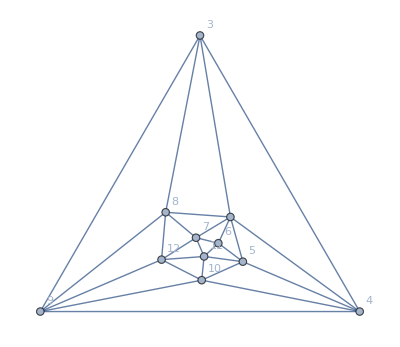

```mathematica
pl3=EdgeContract[pl1,1<->2]
```

```mathematica
EdgeList[pl3]
```

{3<->8,3<->9,3<->4,4<->9,4<->10,4<->5,5<->10,5<->11,5<->6,6<->11,6<->7,7<->11,7<->12,7<->8,8<->12,8<->9,9<->12,9<->10,10<->12,10<->11,11<->12,1<->3,1<->4,1<->5,1<->6,1<->7,1<->8}

```mathematica
ffpl3=FindFullFormula[pl3];
```

```mathematica
Add2[sets_]:=Block[{},SortSets[Table[If[MemberQ[s,1],Sort[Append[s,2]],s],{s,sets}]]]
```

```mathematica
preselect=Select[ffpl3,StringCount[SymbolName[#],"x"]==3&]
```

{v19bx37ax468x5c,v19bx37ax46cx58,v1cx36ax48bx579,v1ax36cx48bx579,v19bx357x4cx68a,v19bx35cx47x68a,v19bx357x46cx8a,v19bx35cx468x7a}

```mathematica
pl3gen=Sort[Table[SetsToSymbol2[SortSets[Add2[SymbolToSets[k]]]],{k,preselect}]]
```

{v129bx357x46cx8a,v129bx357x4cx68a,v129bx35cx468x7a,v129bx35cx47x68a,v129bx37ax468x5c,v129bx37ax46cx58,v12ax36cx48bx579,v12cx36ax48bx579}

```mathematica
Remove12[sets_]:=SortSets[Map[Select[#,!MemberQ[{1,2},#]&]&,sets]]
```

## one by one

```mathematica
pl1gen
```

{v19bx25cx37ax468,v19bx24cx357x68a,v18ax29bx357x46c,v18bx259x37ax46c,v18bx24cx36ax579,v18ax24bx36cx579,v17ax29bx35cx468,v17ax259x36cx48b,v179x25cx36ax48b,v179x24bx35cx68a}

```mathematica
pl1genbis=Map[SetsToSymbol2[#]&,Sort[Map[Remove12[#]&,Map[SymbolToSets[#]&,pl1gen]]]]
```

{v357x4cx68ax9b,v357x46cx8ax9b,v35cx4bx68ax79,v35cx468x7ax9b,v36ax4cx579x8b,v36ax48bx5cx79,v36cx4bx579x8a,v36cx48bx59x7a,v37ax468x5cx9b,v37ax46cx59x8b}

```mathematica
pl2gen
```

{v19bx25cx37ax468,v19bx24cx357x68a,v18ax29bx357x46c,v18bx259x37ax46c,v18bx24cx36ax579,v18ax24bx36cx579,v17ax29bx35cx468,v17ax259x36cx48b,v179x25cx36ax48b,v179x24bx35cx68a,v129bx37ax468x5c,v129bx37ax46cx58,v12cx36ax48bx579,v12ax36cx48bx579,v129bx357x4cx68a,v129bx35cx47x68a,v129bx357x46cx8a,v129bx35cx468x7a}

```mathematica
pl2genbis=Map[SetsToSymbol2[#]&,Sort[Map[Remove12[#]&,Map[SymbolToSets[#]&,pl2gen]]]]
```

{v357x4cx68ax9b,v357x4cx68ax9b,v357x46cx8ax9b,v357x46cx8ax9b,v35cx47x68ax9b,v35cx4bx68ax79,v35cx468x7ax9b,v35cx468x7ax9b,v36ax4cx579x8b,v36ax48bx5cx79,v36ax48bx579xc,v36cx4bx579x8a,v36cx48bx59x7a,v36cx48bx579xa,v37ax468x5cx9b,v37ax468x5cx9b,v37ax46cx58x9b,v37ax46cx59x8b}

```mathematica
pl3gen
```

{v129bx357x46cx8a,v129bx357x4cx68a,v129bx35cx468x7a,v129bx35cx47x68a,v129bx37ax468x5c,v129bx37ax46cx58,v12ax36cx48bx579,v12cx36ax48bx579}

```mathematica
pl3genbis=Map[SetsToSymbol2[#]&,Sort[Map[Remove12[#]&,Map[SymbolToSets[#]&,pl3gen]]]]
```

{v357x4cx68ax9b,v357x46cx8ax9b,v35cx47x68ax9b,v35cx468x7ax9b,v36ax48bx579xc,v36cx48bx579xa,v37ax468x5cx9b,v37ax46cx58x9b}

```mathematica
rep1bis=Table[k->Style[k,Red],{k,Intersection[pl2genbis,pl1genbis]}]
```

{v357x46cx8ax9b→v357x46cx8ax9b,v357x4cx68ax9b→v357x4cx68ax9b,v35cx468x7ax9b→v35cx468x7ax9b,v35cx4bx68ax79→v35cx4bx68ax79,v36ax48bx5cx79→v36ax48bx5cx79,v36ax4cx579x8b→v36ax4cx579x8b,v36cx48bx59x7a→v36cx48bx59x7a,v36cx4bx579x8a→v36cx4bx579x8a,v37ax468x5cx9b→v37ax468x5cx9b,v37ax46cx59x8b→v37ax46cx59x8b}

```mathematica
rep3bis=Table[k->Style[k,Blue],{k,Intersection[pl2genbis,pl3genbis]}]
```

{v357x46cx8ax9b→v357x46cx8ax9b,v357x4cx68ax9b→v357x4cx68ax9b,v35cx468x7ax9b→v35cx468x7ax9b,v35cx47x68ax9b→v35cx47x68ax9b,v36ax48bx579xc→v36ax48bx579xc,v36cx48bx579xa→v36cx48bx579xa,v37ax468x5cx9b→v37ax468x5cx9b,v37ax46cx58x9b→v37ax46cx58x9b}

```mathematica
pl2genbis/.rep1bis/.rep3bis
```

{v357x4cx68ax9b,v357x4cx68ax9b,v357x46cx8ax9b,v357x46cx8ax9b,v35cx47x68ax9b,v35cx4bx68ax79,v35cx468x7ax9b,v35cx468x7ax9b,v36ax4cx579x8b,v36ax48bx5cx79,v36ax48bx579xc,v36cx4bx579x8a,v36cx48bx59x7a,v36cx48bx579xa,v37ax468x5cx9b,v37ax468x5cx9b,v37ax46cx58x9b,v37ax46cx59x8b}

```mathematica
rep1=Table[k->Style[k,Darker[Green]],{k,Intersection[pl2gen,pl1gen]}]
```

{v179x24bx35cx68a→v179x24bx35cx68a,v179x25cx36ax48b→v179x25cx36ax48b,v17ax259x36cx48b→v17ax259x36cx48b,v17ax29bx35cx468→v17ax29bx35cx468,v18ax24bx36cx579→v18ax24bx36cx579,v18ax29bx357x46c→v18ax29bx357x46c,v18bx24cx36ax579→v18bx24cx36ax579,v18bx259x37ax46c→v18bx259x37ax46c,v19bx24cx357x68a→v19bx24cx357x68a,v19bx25cx37ax468→v19bx25cx37ax468}

```mathematica
rep3=Table[k->Style[k,Darker[Yellow]],{k,Intersection[pl2gen,pl3gen]}]
```

{v129bx357x46cx8a→v129bx357x46cx8a,v129bx357x4cx68a→v129bx357x4cx68a,v129bx35cx468x7a→v129bx35cx468x7a,v129bx35cx47x68a→v129bx35cx47x68a,v129bx37ax468x5c→v129bx37ax468x5c,v129bx37ax46cx58→v129bx37ax46cx58,v12ax36cx48bx579→v12ax36cx48bx579,v12cx36ax48bx579→v12cx36ax48bx579}

```mathematica
pl2gen/.rep1/.rep3
```

{v19bx25cx37ax468,v19bx24cx357x68a,v18ax29bx357x46c,v18bx259x37ax46c,v18bx24cx36ax579,v18ax24bx36cx579,v17ax29bx35cx468,v17ax259x36cx48b,v179x25cx36ax48b,v179x24bx35cx68a,v129bx37ax468x5c,v129bx37ax46cx58,v12cx36ax48bx579,v12ax36cx48bx579,v129bx357x4cx68a,v129bx35cx47x68a,v129bx357x46cx8a,v129bx35cx468x7a}

```mathematica
Map[Length,{pl1gen,pl2gen,pl3gen}]
```

{10,18,8}

```mathematica
Map[Length,{pl1genbis,pl2genbis,pl3genbis}]
```

{10,18,8}